```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
```

```mathematica
fitrange={{0,0.00252},{0,0.0045},{0,0.0053},{0,0.0075},{0,0.007},{0,0.009},{0,0.011},{0,0.013},{0,0.015},{0,0.0174},{0,0.021},{0,0.033},{0,0.079}};
fitdata =Table[Select[filterdata[[i, 1]], #[[1]]≥ fitrange[[i,1]] && #[[1]]≤fitrange[[i,2]]&],{i,{1,2,3,4,5,6,7,8,9,10,11,12,13}}];
```

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[13],ImageSize->900,Frame->True]
```

## nlm

```mathematica
startval={{
{a,1.22},{b,-0.05},{μ,0.7},{σ,15},{c,0.1},{d,1}},
{{a,1},{b,0},{μ,1},{σ,10},{c,0.2},{d,7}},
{{a,1.22},{b,-0.05},{μ,1.7},{σ,10},{c,0.15},{d,2}},
{{a,1.22},{b,-0.05},{μ,2.7},{σ,10},{c,0.2},{d,1}},
{{a,1.21},{b,-0.05},{μ,1.3},{σ,15},{c,0.16},{d,1.5}},
{{a,1.2},{b,-0.05},{μ,2.4},{σ,10},{c,0.15},{d,1}},
{{a,1.5},{b,-0.05},{μ,3.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,4.3},{σ,10},{c,0.15},{d,10}},
{{a,1.2},{b,-0.05},{μ,5.4},{σ,20},{c,0.2},{d,1}},
{{a,1.5},{b,-0.05},{μ,6.6},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.1},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,11},{σ,10},{c,0.15},{d,10}},
{{a,1},{b,-0.05},{μ,30},{σ,76},{c,0.15},{d,1}}
};
Conμup={3,3,3,3,3,3,4,5,6,7,7,12,40};
Conddown={1,1,1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.02};
Conσup={100,100,100,100,30,100,19,100,100,100,100,100,100};
Concdown={0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.1};
Conaup={2,2,2,2,2,2,2,2,2,2,2,2,2};
Condup={5,3,3,3,3,3,3,3,3,3,3,3,3};
fitvals={};
nlms={};
Do[
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}],
0.1<a,a<Conaup[[n]],-1<b,b<1,0.5<μ,μ<Conμup[[n]],0.1<σ,σ<Conσup[[n]],Concdown[[n]]<c,c<10,Conddown[[n]]<d,d<Condup[[n]]}, startval[[n]], x];
Quiet[fitvals=Append[fitvals,nlm["ParameterTableEntries"]]];
nlms=Append[nlms,nlm];
Print[n];
Quiet[Print[nlm["ParameterTable"]]],
{n,1,13}]
```

1

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.25176 | 0.00307217 | 407.451 | 2.17379845474×10^-1116
b | -0.0659128 | 0.000748048 | -88.1131 | 1.74631714225×10^-474
μ | 0.71396 | 0.000149643 | 4771.08 | 7.78715823287×10^-2187
σ | 11.5799 | 0.125073 | 92.5854 | 1.08457965481×10^-493
c | 0.136855 | 0.0027062 | 50.5711 | 3.52021×10^-278
d | 2.8771 | 0.105677 | 27.2254 | 1.1906×10^-122

2

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.26605 | 0.00141804 | 892.818 | 2.00404828812×10^-2379
b | -0.0640796 | 0.000324495 | -197.475 | 6.66303846026×10^-1220
μ | 1.84252 | 0.000104956 | 17555.1 | 1.23195745785×10^-4700
σ | 13.1646 | 0.0899851 | 146.298 | 6.62606120273×10^-1000
c | 0.139015 | 0.00119606 | 116.228 | 9.24926165877×10^-838
d | 1.39928 | 0.0311633 | 44.9014 | 8.69865×10^-296

3

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.2555 | 0.00142603 | 880.421 | 1.57209209047×10^-1514
b | -0.0641998 | 0.000383166 | -167.551 | 1.73005850475×10^-762
μ | 1.68946 | 0.00012314 | 13719.8 | 1.78346408772×10^-2772
σ | 14.2953 | 0.106098 | 134.737 | 4.14998695811×10^-667
c | 0.152559 | 0.00122305 | 124.736 | 7.39258845649×10^-634
d | 1.18893 | 0.0217702 | 54.613 | 9.8290366297×10^-310

4

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.25495 | 0.00107579 | 1166.54 | 9.78060773667×10^-2215
b | -0.0637967 | 0.000251137 | -254.031 | 4.19663546153×10^-1232
μ | 2.74457 | 0.000106193 | 25845.2 | 7.10050403662×10^-4226
σ | 15.3241 | 0.0917307 | 167.056 | 1.78536830391×10^-969
c | 0.158857 | 0.00095836 | 165.76 | 1.12110426893×10^-964
d | 1.05204 | 0.0129217 | 81.4164 | 7.32578579552×10^-552

5

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.23004 | 0.00143678 | 856.107 | 6.6185123097×10^-1053
b | -0.0635696 | 0.000500513 | -127.009 | 3.54272704234×10^-483
μ | 1.30738 | 0.000156042 | 8378.36 | 2.97629991912×10^-1741
σ | 17.0919 | 0.134817 | 126.779 | 1.18527910113×10^-482
c | 0.176514 | 0.00124432 | 141.856 | 2.62840958325×10^-515
d | 0.956589 | 0.0129624 | 73.7971 | 4.82197658593×10^-331

6

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.24411 | 0.0014504 | 857.774 | 5.78319300738×10^-1307
b | -0.0634506 | 0.000408386 | -155.369 | 1.06741989676×10^-649
μ | 2.40147 | 0.000173876 | 13811.4 | 7.13212608865×10^-2387
σ | 17.686 | 0.15037 | 117.616 | 1.34383262079×10^-546
c | 0.172385 | 0.00129569 | 133.044 | 6.51710095034×10^-592
d | 0.849448 | 0.0121282 | 70.0388 | 1.79577832122×10^-365

7

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21379 | 0.00228385 | 531.464 | 1.4078788782×10^-1323
b | -0.0631777 | 0.000529868 | -119.233 | 1.51291455634×10^-629
μ | 3.41978 | 0.000287878 | 11879.3 | 3.67315730247×10^-2800
σ | 19. | 0.248795 | 76.3682 | 6.26073287216×10^-441
c | 0.196116 | 0.00211364 | 92.7858 | 4.23346396182×10^-521
d | 0.903885 | 0.0165853 | 54.4992 | 3.62619091883×10^-314

8

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21176 | 0.00128946 | 939.743 | 1.20681333889×10^-1837
b | -0.0642021 | 0.000278966 | -230.143 | 9.24437293196×10^-1053
μ | 4.3544 | 0.000172253 | 25279.1 | 9.18402241904×10^-3689
σ | 19.279 | 0.148935 | 129.446 | 2.92652788315×10^-743
c | 0.195075 | 0.00120478 | 161.918 | 8.99999000275×10^-862
d | 0.841638 | 0.00867674 | 96.9993 | 2.75908958156×10^-596

9

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21268 | 0.00123794 | 979.594 | 1.73804258049×10^-2101
b | -0.0632328 | 0.000251211 | -251.711 | 2.77192099688×10^-1226
μ | 5.40095 | 0.000181234 | 29801. | 2.42102151087×10^-4318
σ | 21.1753 | 0.156558 | 135.255 | 6.30051371536×10^-841
c | 0.197017 | 0.00116221 | 169.519 | 1.6699087857×10^-978
d | 0.77499 | 0.00756383 | 102.46 | 2.44309601001×10^-678

10

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20997 | 0.00118638 | 1019.88 | 8.20596282795×10^-2413
b | -0.0639143 | 0.000224115 | -285.185 | 6.05976298812×10^-1460
μ | 6.62914 | 0.000182646 | 36295.1 | 1.08925865211×10^-5103
σ | 22. | 0.158087 | 139.163 | 1.12673575078×10^-943
c | 0.201719 | 0.00112265 | 179.681 | 1.27046498242×10^-1123
d | 0.740169 | 0.00666173 | 111.108 | 3.11467851724×10^-791

11

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19587 | 0.00227206 | 526.337 | 2.78538121614×10^-1055
b | -0.0630681 | 0.000502125 | -125.602 | 1.74343221523×10^-544
μ | 5.12695 | 0.000419556 | 12219.9 | 3.48214188206×10^-2195
σ | 28.5712 | 0.360657 | 79.2197 | 1.25053538658×10^-390
c | 0.21287 | 0.00216214 | 98.453 | 8.5820903338×10^-462
d | 0.677822 | 0.010218 | 66.3361 | 4.15525602242×10^-335

12

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19099 | 0.00225085 | 529.128 | 1.64512660038×10^-1534
b | -0.0631809 | 0.000350093 | -180.469 | 3.73749701161×10^-930
μ | 11.1138 | 0.000489377 | 22710. | 4.0609257573×10^-3680
σ | 35.8301 | 0.419845 | 85.3412 | 1.59139996824×10^-538
c | 0.218257 | 0.00218553 | 99.8644 | 2.94875860434×10^-616
d | 0.62305 | 0.00882722 | 70.5828 | 1.4449804433×10^-449

13

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.22171 | 0.00289936 | 421.373 | 1.96056934913×10^-1621
b | -0.062594 | 0.000295847 | -211.576 | 5.42916299276×10^-1159
μ | 29.7481 | 0.00101328 | 29358.2 | 3.06326534599×10^-4521
σ | 76.5728 | 0.850917 | 89.9886 | 3.73518581797×10^-623
c | 0.190548 | 0.00285631 | 66.7111 | 3.09230862645×10^-461
d | 0.458366 | 0.00885875 | 51.7416 | 5.36523763182×10^-342

## nlm2

```mathematica
startval={{
{a,1.22},{b,-0.05},{μ,0.7},{σ,15},{c,0.1},{d,1}},
{{a,1},{b,0},{μ,1},{σ,10},{c,0.2},{d,7}},
{{a,1.22},{b,-0.05},{μ,1.7},{σ,10},{c,0.15},{d,2}},
{{a,1.22},{b,-0.05},{μ,2.7},{σ,10},{c,0.2},{d,1}},
{{a,1.21},{b,-0.05},{μ,1.3},{σ,15},{c,0.16},{d,1.5}},
{{a,1.2},{b,-0.05},{μ,2.4},{σ,10},{c,0.15},{d,1}},
{{a,1.5},{b,-0.05},{μ,3.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,4.3},{σ,10},{c,0.15},{d,10}},
{{a,1.2},{b,-0.05},{μ,5.4},{σ,20},{c,0.2},{d,1}},
{{a,1.5},{b,-0.05},{μ,6.6},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.1},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,11},{σ,10},{c,0.15},{d,10}},
{{a,1},{b,-0.05},{μ,30},{σ,76},{c,0.15},{d,1}}
};
Conμup={3,3,3,3,3,3,4,5,6,7,7,12,40};
Conddown={1,1,1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.02};
Conσup={100,100,100,100,30,100,19,100,100,100,100,100,100};
Concdown={0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.1};
Conaup={2,2,2,2,2,2,2,2,2,2,2,2,1.18};
Condup={100,100,100,3,3,3,3,3,3,3,3,3,3};
fitvals2={};
nlms2={};
Do[
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}],
0.1<a,a<Conaup[[n]],-1<b,b<1,0.5<μ,μ<Conμup[[n]],0.1<σ,σ<Conσup[[n]],Concdown[[n]]<c,c<10,Conddown[[n]]<d,d<Condup[[n]]}, startval[[n]], x];
Quiet[fitvals2=Append[fitvals2,nlm["ParameterTableEntries"]]];
nlms2=Append[nlms2,nlm];
Print[n];
Quiet[Print[nlm["ParameterTable"]]],
{n,{13}}]
nlms[[13]]=nlm;
Quiet[fitvals[[13]]=nlm["ParameterTableEntries"]];
```

13

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.18 | 0.00354768 | 332.611 | 1.90155677451×10^-1461
b | -0.0621705 | 0.000313246 | -198.472 | 7.68174233842×10^-1117
μ | 29.7418 | 0.0011068 | 26871.8 | 1.04239156502×10^-4460
σ | 72.5396 | 0.918348 | 78.9892 | 3.62800209035×10^-550
c | 0.231334 | 0.00350637 | 65.9753 | 1.19820590742×10^-455
d | 0.560962 | 0.0105641 | 53.1006 | 2.83981509577×10^-353

{1.87904,2.99648,4.01354,5.02443,5.99862,7.06453,8.05022,9.0256,10.0091,11.2309,16.7331,22.6462,52.0119}

{1.18082,1.19111,1.16714,1.15989,1.1171,1.13518,1.08085,1.08089,1.0789,1.07216,1.04607,1.03591,1.09376}

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.26165 | 1.62634 | 3.23528 | 0.00894059
min | 1.05344 | 0.0153109 | 68.8032 | 1.02521×10^-14
amp | 0.218059 | 0.0376463 | 5.79232 | 0.000174777

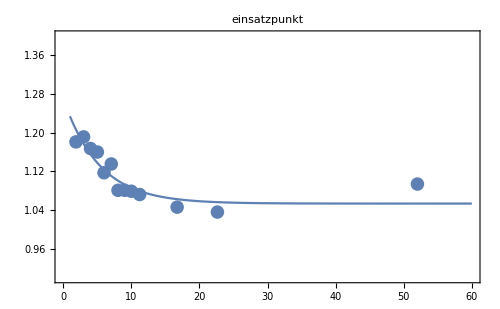

{0.0940891,0.0946233,0.103622,0.10751,0.120067,0.11648,0.133133,0.13261,0.133759,0.136703,0.144632,0.148229,0.129198}

| Estimate | Standard Error | t-Statistic | P-Value
a | 6.99857 | 1.40222 | 4.99108 | 0.000748027
min | 0.152939 | 0.00530416 | 28.8338 | 3.53693×10^-10
amp | 0.0836788 | 0.00593888 | 14.09 | 1.94035×10^-7

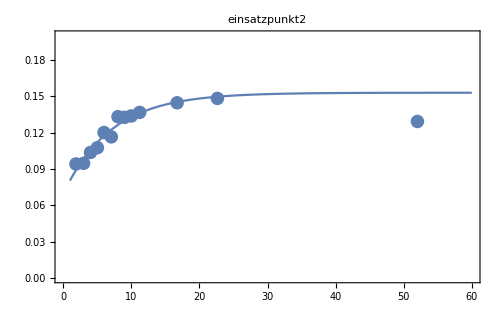

| Estimate | Standard Error | t-Statistic | P-Value
a | 8.00001 | 6.22159 | 1.28585 | 0.230593
min | 0.174606 | 0.594027 | 0.293936 | 0.775473
amp | 2.19891 | 0.555721 | 3.95685 | 0.00332006

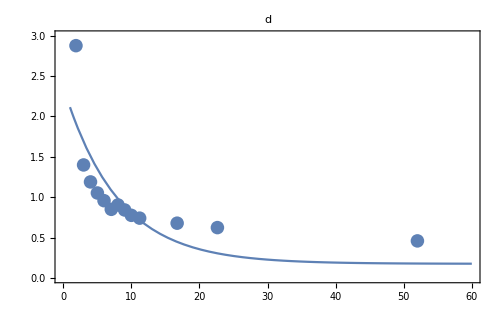

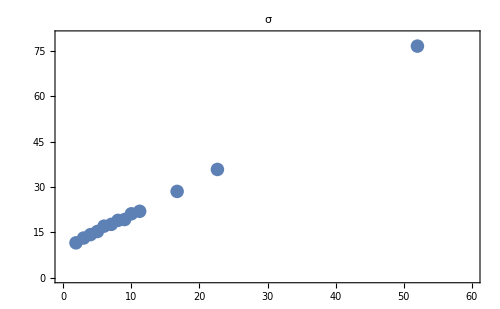

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.78139 | 2.40045 | 2.40846 | 0.03678
min | 1.20029 | 0.00957938 | 125.3 | 2.57234×10^-17
amp | 0.0950161 | 0.0208123 | 4.56539 | 0.00103355

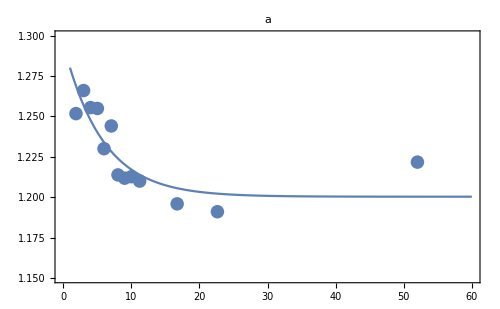

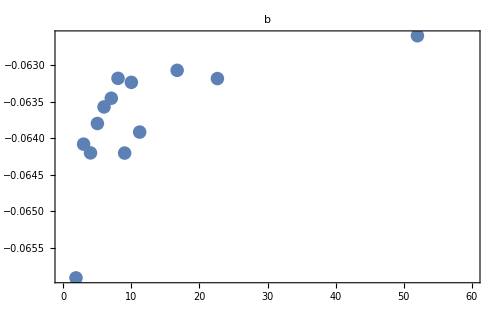

| Estimate | Standard Error | t-Statistic | P-Value
min | 0.0996385 | 0.00969893 | 10.2732 | 2.85798×10^-6
amp | 0.124917 | 0.00829483 | 15.0596 | 1.08988×10^-7
a | 6.77521 | 1.23714 | 5.47649 | 0.000391942

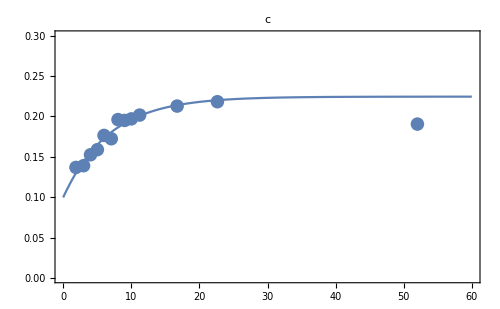

```mathematica
steigpunkt=fitvals[[All,3,1]];
fallpunkt={{{0.002593,0.6409}},{{0.004839,0.6786}},{{0.005703,0.6157}},{{0.007769,0.7189}},{{0.007306,0.7321}},{{0.009466,0.7529}},{{0.01147,0.7529}},{{0.01338,0.672}},{{0.01541,0.6945}},{{0.01786,0.6394}},{{0.02186,0.6795}},{{0.03376,0.6269}},{{0.08176,0.647}}}[[All,1,1]]*10^3;
T=fallpunkt-steigpunkt

einsatzpunkt=fitvals[[All,1,1]]-fitvals[[All,2,1]]-fitvals[[All,5,1]]

nlmeinsatzpunkt=NonlinearModelFit[Transpose[{T,einsatzpunkt}],{min+amp Exp[-x/a],0<amp,amp<1,0<min,0<a},{a,min,amp},x];
Quiet[nlmeinsatzpunkt["ParameterTable"]]
Show[Plot[Normal[nlmeinsatzpunkt],{x,1,60},PlotLabel->"einsatzpunkt",Frame->True,PlotRange->{{0,60},{0.9,1.4}},ImageSize->500],ListPlot[Transpose[{T,einsatzpunkt}]]]

einsatzpunkt2=fitvals[[All,5,1]]/(fitvals[[All,1,1]]-fitvals[[All,2,1]]+fitvals[[All,5,1]])

nlmeinsatzpunkt2=NonlinearModelFit[Drop[Transpose[{T,einsatzpunkt2}],-1],{min-amp Exp[-x/a],0<amp,amp<1,0<min,0<a},{a,min,amp},x];
Quiet[nlmeinsatzpunkt2["ParameterTable"]]
Show[Plot[Normal[nlmeinsatzpunkt2],{x,1,60},PlotLabel->"einsatzpunkt2",Frame->True,PlotRange->{{0,60},{0,0.2}},ImageSize->500],ListPlot[Transpose[{T,einsatzpunkt2}]]]


nlmd=NonlinearModelFit[Drop[Transpose[{T,fitvals[[All,6,1]]}],-1],{min+amp Exp[-x/a],0<amp,amp<100,0<min,8<a},{a,min,amp},x];
Quiet[nlmd["ParameterTable"]]
Show[Plot[Normal[nlmd],{x,1,60},PlotLabel->"d",Frame->True,PlotRange->{{0,60},{0,3}},ImageSize->500],ListPlot[Transpose[{T,fitvals[[All,6,1]]}]]]


ListPlot[Transpose[{T,fitvals[[All,4,1]]}],PlotLabel->"σ",Frame->True,PlotRange->{{0,60},{0,80}}]


nlma=NonlinearModelFit[Transpose[{T,fitvals[[All,1,1]]}],{min+amp Exp[-x/a],0<amp,amp<2,0<min,2<a},{a,min,amp},x];
Quiet[nlma["ParameterTable"]]
Show[Plot[Normal[nlma],{x,1,60},PlotLabel->"a",Frame->True,PlotRange->{{0,60},{1.15,1.3}},ImageSize->500],ListPlot[Transpose[{T,fitvals[[All,1,1]]}]]]


ListPlot[Transpose[{T,fitvals[[All,2,1]]}],PlotLabel->"b",Frame->True,PlotRange->{{0,60},Automatic}]


nlmc=NonlinearModelFit[Drop[Transpose[{T,fitvals[[All,5,1]]}],-1],{min+amp(1- Exp[-x/a]),0<min,0<amp,0<a},{min,amp,a},x];
Quiet[nlmc["ParameterTable"]]
Show[Plot[Normal[nlmc],{x,0,60},PlotLabel->"c",Frame->True,PlotRange->{{0,60},{0,0.3}}],ListPlot[Transpose[{T,fitvals[[All,5,1]]}]]]
```

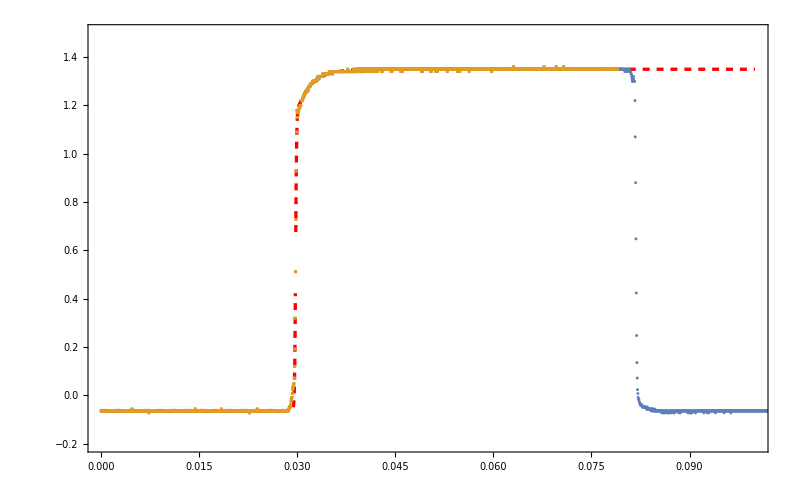

```mathematica
nr=13;
Show[Plot[Normal[nlms[[nr]]],{x,0,0.1},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed,Thickness->0.003}],ListPlot[{filterdata[[nr,1]],fitdata[[nr]]},PlotMarkers->{Automatic,3}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm],a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}]},{x,0,0.01},ImageSize->600,Frame->True,PlotRange->{-0.2,1.5},Frame->True, PlotStyle->{Red, Dashed,3}],ListPlot[{filterdata[[n,1]],fitdata[[n]]},PlotMarkers->{Automatic,1}]],{{a,1.23},0,5},{{b,0.05},-2,2},{{μ,1.8},0.7,3},{{σ,10},1,20},{{c,0.11},0,2},{{d,9300},0,10000}]
```

```mathematica
exp=Prepend[Transpose[{
Table[0,{13}],
fitrange[[All,2]],
fitvals[[All,1,1]],
Table[0.1,{13}],
Conaup,
fitvals[[All,2,1]],
Table[-1,{13}],
Table[1,{13}],
fitvals[[All,3,1]],
Table[0.5,{13}],
Conμup,
fitvals[[All,4,1]],
Table[0.1,{13}],
Conσup,
fitvals[[All,5,1]],
Concdown,
Table[10,{13}],
fitvals[[All,6,1]],
Conddown,
Condup
}],{"startrange","endrange","Astart","Ad","Au","ustart","ud","uu","μstart","μd","μu","σstart","σd","σu","Bstart","Bd","Bu","λstart","λd","λu"}];
exp//TableForm
```

startrange | endrange | Astart | Ad | Au | ustart | ud | uu | μstart | μd | μu | σstart | σd | σu | Bstart | Bd | Bu | λstart | λd | λu
0 | 0.00252 | 1.25176 | 0.1 | 2 | -0.0659128 | -1 | 1 | 0.71396 | 0.5 | 3 | 11.5799 | 0.1 | 100 | 0.136855 | 0.001 | 10 | 2.8771 | 1 | 5
0 | 0.0045 | 1.26605 | 0.1 | 2 | -0.0640796 | -1 | 1 | 1.84252 | 0.5 | 3 | 13.1646 | 0.1 | 100 | 0.139015 | 0.001 | 10 | 1.39928 | 1 | 3
0 | 0.0053 | 1.2555 | 0.1 | 2 | -0.0641998 | -1 | 1 | 1.68946 | 0.5 | 3 | 14.2953 | 0.1 | 100 | 0.152559 | 0.001 | 10 | 1.18893 | 1 | 3
0 | 0.0075 | 1.25495 | 0.1 | 2 | -0.0637967 | -1 | 1 | 2.74457 | 0.5 | 3 | 15.3241 | 0.1 | 100 | 0.158857 | 0.001 | 10 | 1.05204 | 0.1 | 3
0 | 0.007 | 1.23004 | 0.1 | 2 | -0.0635696 | -1 | 1 | 1.30738 | 0.5 | 3 | 17.0919 | 0.1 | 30 | 0.176514 | 0.001 | 10 | 0.956589 | 0.1 | 3
0 | 0.009 | 1.24411 | 0.1 | 2 | -0.0634506 | -1 | 1 | 2.40147 | 0.5 | 3 | 17.686 | 0.1 | 100 | 0.172385 | 0.001 | 10 | 0.849448 | 0.1 | 3
0 | 0.011 | 1.21379 | 0.1 | 2 | -0.0631777 | -1 | 1 | 3.41978 | 0.5 | 4 | 19. | 0.1 | 19 | 0.196116 | 0.001 | 10 | 0.903885 | 0.1 | 3
0 | 0.013 | 1.21176 | 0.1 | 2 | -0.0642021 | -1 | 1 | 4.3544 | 0.5 | 5 | 19.279 | 0.1 | 100 | 0.195075 | 0.001 | 10 | 0.841638 | 0.1 | 3
0 | 0.015 | 1.21268 | 0.1 | 2 | -0.0632328 | -1 | 1 | 5.40095 | 0.5 | 6 | 21.1753 | 0.1 | 100 | 0.197017 | 0.001 | 10 | 0.77499 | 0.1 | 3
0 | 0.0174 | 1.20997 | 0.1 | 2 | -0.0639143 | -1 | 1 | 6.62914 | 0.5 | 7 | 22. | 0.1 | 100 | 0.201719 | 0.001 | 10 | 0.740169 | 0.1 | 3
0 | 0.021 | 1.19587 | 0.1 | 2 | -0.0630681 | -1 | 1 | 5.12695 | 0.5 | 7 | 28.5712 | 0.1 | 100 | 0.21287 | 0.001 | 10 | 0.677822 | 0.1 | 3
0 | 0.033 | 1.19099 | 0.1 | 2 | -0.0631809 | -1 | 1 | 11.1138 | 0.5 | 12 | 35.8301 | 0.1 | 100 | 0.218257 | 0.001 | 10 | 0.62305 | 0.1 | 3
0 | 0.079 | 1.22171 | 0.1 | 2 | -0.062594 | -1 | 1 | 29.7481 | 0.5 | 40 | 76.5728 | 0.1 | 100 | 0.190548 | 0.1 | 10 | 0.458366 | 0.02 | 3

```mathematica
Export[NotebookDirectory[]<>"FitdataRoot.txt",Drop[exp,1],"Table"];
```